# a-Y Phase Spaces and Potentials

## Define Variables and Parameters

```mathematica
(*Clear all variables*)
ClearAll["Global`*"];
```

```mathematica
(*Dark matter (z), radiation (v) and dark energy x written in terms of the scale factor a*)
ca[x0_]=(1-x0)/(x0-R);

x[a_,x0_]=(a^(-3*(1-R))+ca[x0]*R)/(a^(-3*(1-R))+ca[x0]);

z[a_,x0_,c_]=c*((x[a,x0]-R)/(1-x[a,x0]))^(1/(1-R));

v[a_,x0_,cv_]=cv*((x[a,x0]-R)/(1-x[a,x0]))^(4/(3*(1-R)));
```

```mathematica
(*Define R and cv*)
R=0.05;
cv=0.000034;
```

```mathematica
(*Define w, the resulting term left in y' when y = 0, which needs to be solved to find the Einstein fixed points*)
(*When w = 0, there is an Einstein fixed point*)
w[a_,x0_,c_,cv_]=z[a,x0,c]+2*v[a,x0,cv]-3*R+x[a,x0]*(1+3*R)-3*x[a,x0]^2;
```

```mathematica
(*Import values of c*)
c=Flatten[Import["G:\\My Drive\\Wolfram Mathematica\\Project 1\\Non_Interacting_Matter\\Compact_Variables\\Full_Case\\x_Y_Z_R0.05\\cValues.csv"]]
```

{0.05,0.200851,0.25,0.319517,0.35,0.386125,0.5}

## Find the Einstein Points in Each Case

```mathematica
(*Numerically solve w = 0 to find the Einstein fixed points in each case*)
(*FindRoot is a Newtonian approximation*)
```

### One Einstein Point: c1

```mathematica
aOneEinsteinPointc1=FindRoot[w[a,0.2,c[[1]],cv]==0,{a,0.2}];
```

```mathematica
(*Remove the arrow from the solution above*)
aOneEinsteinPointc1=a/.aOneEinsteinPointc1
```

0.1668

### Two Einstein Points: c2 (1st Limiting Case)

```mathematica
aTwoEinsteinPointsc2i=FindRoot[w[a,0.1,c[[2]],cv]==0,{a,0.1}];
aTwoEinsteinPointsc2ii=FindRoot[w[a,0.1,c[[2]],cv]==0,{a,0.9}];
```

```mathematica
(*Put the Einstein points into one variable name for this case*)
aTwoEinsteinPointsc2={a/.aTwoEinsteinPointsc2i,a/.aTwoEinsteinPointsc2ii}
```

{0.188558,0.581076}

### Three Einstein Points: c3

```mathematica
aThreeEinsteinPointsc3i=FindRoot[w[a,0.08,c[[3]],cv]==0,{a,0.1}];
aThreeEinsteinPointsc3ii=FindRoot[w[a,0.08,c[[3]],cv]==0,{a,0.4}];
aThreeEinsteinPointsc3iii=FindRoot[w[a,0.08,c[[3]],cv]==0,{a,0.9}];
```

```mathematica
(*Put the Einstein points into one variable name for this case*)
aThreeEinsteinPointsc3={a/.aThreeEinsteinPointsc3i,a/.aThreeEinsteinPointsc3ii,a/.aThreeEinsteinPointsc3iii}
```

{0.174822,0.402707,0.555175}

### Three Einstein Points: c4

```mathematica
aThreeEinsteinPointsc4i=FindRoot[w[a,0.08,c[[4]],cv]==0,{a,0.1}];
aThreeEinsteinPointsc4ii=FindRoot[w[a,0.08,c[[4]],cv]==0,{a,0.4}];
aThreeEinsteinPointsc4iii=FindRoot[w[a,0.08,c[[4]],cv]==0,{a,0.6}];
```

```mathematica
(*Put the Einstein points into one variable name for this case*)
aThreeEinsteinPointsc4={a/.aThreeEinsteinPointsc4i,a/.aThreeEinsteinPointsc4ii,a/.aThreeEinsteinPointsc4iii}
```

{0.204402,0.348764,0.594926}

### Three Einstein Points: c5

```mathematica
aThreeEinsteinPointsc5i=FindRoot[w[a,0.08,c[[5]],cv]==0,{a,0.1}];
aThreeEinsteinPointsc5ii=FindRoot[w[a,0.08,c[[5]],cv]==0,{a,0.4}];
aThreeEinsteinPointsc5iii=FindRoot[w[a,0.08,c[[5]],cv]==0,{a,0.6}];
```

```mathematica
(*Put the Einstein points into one variable name for this case*)
aThreeEinsteinPointsc5={a/.aThreeEinsteinPointsc5i,a/.aThreeEinsteinPointsc5ii,a/.aThreeEinsteinPointsc5iii}
```

{0.221488,0.324423,0.608378}

### Two Einstein Points: c6 (2nd Limiting Case)

```mathematica
aTwoEinsteinPointsc6i=FindRoot[w[a,0.9,c[[6]],cv]==0,{a,2}];
aTwoEinsteinPointsc6ii=FindRoot[w[a,0.9,c[[6]],cv]==0,{a,6}];
```

```mathematica
(*Put the Einstein points into one variable name for this case*)
aTwoEinsteinPointsc6={a/.aTwoEinsteinPointsc6i,a/.aTwoEinsteinPointsc6ii}
```

{1.89688,4.38503}

### One Einstein Point: c7

```mathematica
aOneEinsteinPointc7=FindRoot[w[a,0.9,c[[7]],cv]==0,{a,0.1}];
```

```mathematica
(*Remove the arrow from the solution above*)
aOneEinsteinPointc7=a/.aOneEinsteinPointc7
```

4.64873

## Define Variables for Phase Spaces and Potentials

### Phase Spaces

```mathematica
(*Define the Flat Friedmann Separatrix (FFS)*)
(*Define ffs = y^2*)
ffs[a_,x0_]=(1/3)*(x[a,x0]+z[a,x0,c]+v[a,x0,cv]);
```

```mathematica
(*Rearrange for y*)
FFS[a_,x0_]=Sqrt[ffs[a,x0]];
```

```mathematica
(*Define the Closed Friedmann Separatrix (CFS)*)
(*Define cfs = y^2*)
(*aE denotes the a value of the Einstein fixed point*)
cfs[a_,aE_,x0_]= x[a,x0]/3+z[a,x0,c]/3+v[a,x0,cv]/3-((aE/a)^2)*(x[aE,x0]/3+z[aE,x0,c]/3+v[aE,x0,cv]/3);
```

```mathematica
(*Rearrange above equation for y*)
CFS[a_,aE_,x0_]=Sqrt[cfs[a,aE,x0]];
```

```mathematica
(*Define the acceleration*)
Accn=z[a,x0,c]+x+2*v[a,x0,cv]-3*R+3*R*x[a,x0]-3*x[a,x0]^2;
```

### Potentials

```mathematica
(*a0 = 1 today*)
a0=1;
```

```mathematica
(*Define the potential*)
U[a_,x0_]=-(a^2/6)*(x[a,x0]+z[a,x0,c]+v[a,x0,cv]);
```

```mathematica
(*Define the energy of the trajectories from the phase space*)
Energy[x0_,y0_]=-(x[a0,x0]/6+z[a0,x0,c]/6+v[a0,x0,cv]/6-y0^2/2);
```

## One Einstein Point: c1

### Phase Space

```mathematica
(*Trajectories for the phase space*)

trajc1[y0_,x0_]:=y^2==x[a,x0]/3+z[a,x0,c[[1]]]/3+v[a,x0,cv]/3-(1/a^2)*(x[a0,x0]/3+z[a0,x0,c[[1]]]/3+v[a0,x0,cv]/3-y0^2);
```

```mathematica
c1traj[1]=ContourPlot[Evaluate[trajc1[0,0.2]],{a,0,aOneEinsteinPointc1},{y,-1.5,1.5},PlotPoints->100,ContourStyle -> {{Blue, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c1traj[2]=ContourPlot[Evaluate[trajc1[0,0.2]],{a,aOneEinsteinPointc1,3},{y,-1.5,1.5},PlotPoints->100,ContourStyle -> {{Blue, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c1traj[3]=ContourPlot[Evaluate[trajc1[0.12,0.2]],{a,0,aOneEinsteinPointc1},{y,-1.5,1.5},PlotPoints->100,ContourStyle -> {{Magenta, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c1traj[4]=ContourPlot[Evaluate[trajc1[0.12,0.2]],{a,aOneEinsteinPointc1,3},{y,-1.5,1.5},PlotPoints->100,ContourStyle -> {{Magenta, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c1traj[5]=ContourPlot[Evaluate[trajc1[0.18,0.2]],{a,0,aOneEinsteinPointc1},{y,-1.5,1.5},PlotPoints->100,ContourStyle -> {{Purple, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c1traj[6]=ContourPlot[Evaluate[trajc1[0.18,0.2]],{a,aOneEinsteinPointc1,3},{y,-1.5,1.5},PlotPoints->100,ContourStyle -> {{Purple, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c1traj[7]=ContourPlot[Evaluate[trajc1[0.23,0.2]],{a,0,3},{y,-1.5,0},PlotPoints->100,ContourStyle -> {{Orange, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c1traj[8]=ContourPlot[Evaluate[trajc1[0.23,0.2]],{a,0,3},{y,0,1.5},PlotPoints->100,ContourStyle -> {{Orange, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c1traj[9]=ContourPlot[Evaluate[trajc1[0.58,0.2]],{a,0,3},{y,0,1.5},PlotPoints->100,ContourStyle -> {{Pink, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c1traj[10]=ContourPlot[Evaluate[trajc1[0.58,0.2]],{a,0,3},{y,-1.5,0},PlotPoints->100,ContourStyle -> {{Pink, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c1traj[11]=ContourPlot[Evaluate[trajc1[2.06,0.2]],{a,0,3},{y,0,1.5},PlotPoints->100,ContourStyle -> {{Brown, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c1traj[12]=ContourPlot[Evaluate[trajc1[2.06,0.2]],{a,0,3},{y,-1.5,0},PlotPoints->100,ContourStyle -> {{Brown, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
(*Add trajectories into a table*)
Trajc1=Table[c1traj[i],{i,1,12}];
```

```mathematica
(*Plot the FFS*)
(*Plot + and - FFS as a Sqrt was taken and Mathematica defaults to the + only*)
FFSc1=Plot[{FFS[a,0.2][[1]],-FFS[a,0.2][[1]]},{a,0,3},PlotStyle->{{RGBColor[0.21,0.71,0.52],Thickness[0.008]}},PlotRange->All];
```

```mathematica
(*Plot the CFS*)
(*Plot + and - CFS as a Sqrt was taken and Mathematica defaults to the + only*)
CFSc1=Plot[{CFS[a,aOneEinsteinPointc1,0.2][[1]],-CFS[a,aOneEinsteinPointc1,0.2][[1]]},{a,0,3},PlotStyle->{Black},PlotRange->All];
```

```mathematica
(*Plot the Einstein fixed points for this case*)
Einsteinc1=ListPlot[{{aOneEinsteinPointc1,0}},PlotStyle->{Black}];
```

```mathematica
(*Plot the accn = 0 curve for this case*)
Accnc1=ContourPlot[Accn[[1]]==0,{a,0,3},{y,-1.5,1.5},ContourStyle->{Red, Thick}];
```

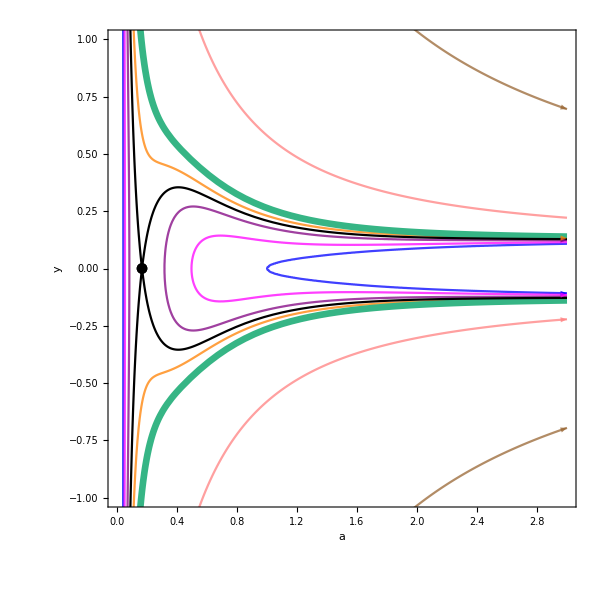

```mathematica
(*Show all components of plots*)
PhaseSpacec1=Show[Trajc1,FFSc1,CFSc1,Einsteinc1,PlotRange->{-1,1},FrameLabel->{"a",Rotate["y",270Degree]},AspectRatio->1,ImageSize->{600,600},BaseStyle->{FontSize->14}]
```

### Potential

```mathematica
(*Plot the potential for this case*)
Uc1=Plot[{U[a,0.2][[1]]},{a,0,3},AxesLabel->{"x","U"},PlotStyle->{Black}];
```

```mathematica
(*Plot the energy from each trajectory in the phase space*)
```

```mathematica
c1Energy[1]=Plot[{Energy[0.2,0][[1]]},{a,0,0.04},AxesLabel->{"x","U"},PlotStyle->{Blue,Opacity[0.75]}];
```

```mathematica
c1Energy[2]=Plot[{Energy[0.2,0][[1]]},{a,1,3},AxesLabel->{"x","U"},PlotStyle->{Blue,Opacity[0.75]}];
```

```mathematica
c1Energy[3]=Plot[{Energy[0.2,0.12][[1]]},{a,0,0.055},AxesLabel->{"x","U"},PlotStyle->{Magenta,Opacity[0.75]}];
```

```mathematica
c1Energy[4]=Plot[{Energy[0.2,0.12][[1]]},{a,0.5,3},AxesLabel->{"x","U"},PlotStyle->{Magenta,Opacity[0.75]}];
```

```mathematica
c1Energy[5]=Plot[{Energy[0.2,0.18][[1]]},{a,0,0.08},AxesLabel->{"x","U"},PlotStyle->{Purple,Opacity[0.75]}];
```

```mathematica
c1Energy[6]=Plot[{Energy[0.2,0.18][[1]]},{a,0.32,3},AxesLabel->{"x","U"},PlotStyle->{Purple,Opacity[0.75]}];
```

```mathematica
c1Energy[7]=Plot[{Energy[0.2,0.23][[1]]},{a,0,3},AxesLabel->{"x","U"},PlotStyle->{Orange,Opacity[0.75]}];
```

```mathematica
c1Energy[8]=Plot[{Energy[0.2,0.58][[1]]},{a,0,3},AxesLabel->{"x","U"},PlotStyle->{Pink,Opacity[0.75]}];
```

```mathematica
c1Energy[9]=Plot[{Energy[0.2,2.06][[1]]},{a,0,3},AxesLabel->{"x","U"},PlotStyle->{Brown,Dashed,Opacity[0.75]}];
```

```mathematica
(*Energy of a trajectory that follows the FFS*)
c1Energy[10]=Plot[{0},{a,0,3},AxesLabel->{"x","U"},PlotStyle->{RGBColor[0.21,0.71,0.52],Thickness[0.008]}];
```

```mathematica
(*Plot dashed black lines between trajectories of the same energy*)
```

```mathematica
c1Energy[11]=Plot[{Energy[0.2,0][[1]]},{a,0.04,1},AxesLabel->{"x","U"},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
c1Energy[12]=Plot[{Energy[0.2,0.12][[1]]},{a,0.055,0.5},AxesLabel->{"x","U"},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
c1Energy[13]=Plot[{Energy[0.2,0.18][[1]]},{a,0.08,0.32},AxesLabel->{"x","U"},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
(*Add energies into a table*)
Energyc1=Table[c1Energy[i],{i,1,13}];
```

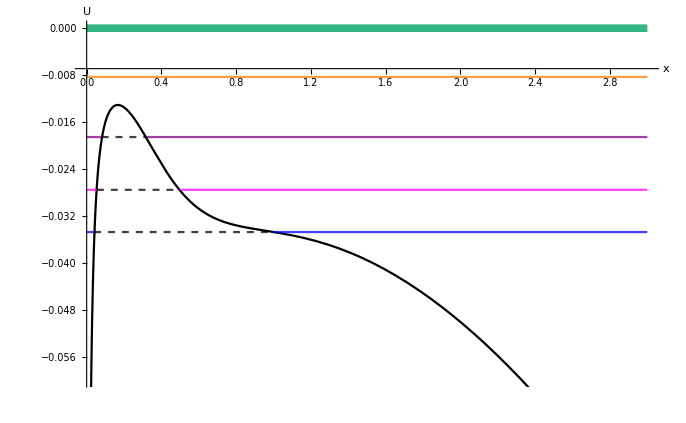

```mathematica
(*Show the potential and energy of the trajectories together*)
Potentialc1=Show[Uc1,Energyc1,ImageSize->{600,400},BaseStyle->{FontSize->14},PlotRange->{-0.06,0}]
```

### Final Plot

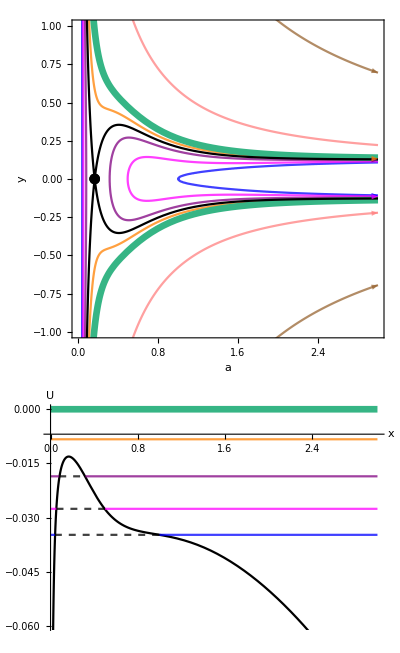

```mathematica
(*Plot the phase space and potential together*)
ayc1=GraphicsColumn[{PhaseSpacec1,Potentialc1},Spacings->{0,-20}]
```

```mathematica
(*Export["G:\\My Drive\\Wolfram Mathematica\\Project 1\\Non_Interacting_Matter\\Compact_Variables\\Full_Case\\x_Y_Z_R0.05\\Figures\\ay_Plots\\ayc1.pdf",ayc1]*)
```

## Two Einstein Points: c2

### Phase Space

```mathematica
(*Trajectories for the phase space*)
trajc2[y0_,x0_]:=y^2==x[a,x0]/3+z[a,x0,c[[2]]]/3+v[a,x0,cv]/3-(1/a^2)*(x[a0,x0]/3+z[a0,x0,c[[2]]]/3+v[a0,x0,cv]/3-y0^2);
```

```mathematica
c2traj[1]=ContourPlot[Evaluate[trajc2[0,0.1]],{a,0,aTwoEinsteinPointsc2[[1]]},{y,-1.5,1.5},PlotPoints->100,ContourStyle -> {{Blue, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c2traj[2]=ContourPlot[Evaluate[trajc2[0,0.1]],{a,aTwoEinsteinPointsc2[[2]],1.5},{y,-1.5,1.5},PlotPoints->100,ContourStyle -> {{Blue, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c2traj[3]=ContourPlot[Evaluate[trajc2[0.07,0.1]],{a,0,aTwoEinsteinPointsc2[[1]]},{y,-1.5,1.5},PlotPoints->100,ContourStyle -> {{Magenta, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c2traj[4]=ContourPlot[Evaluate[trajc2[0.07,0.1]],{a,aTwoEinsteinPointsc2[[1]],1.5},{y,-1.5,1.5},PlotPoints->100,ContourStyle -> {{Magenta, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c2traj[5]=ContourPlot[Evaluate[trajc2[0.09,0.1]],{a,0,aTwoEinsteinPointsc2[[1]]},{y,-1.5,1.5},PlotPoints->100,ContourStyle -> {{Purple, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c2traj[6]=ContourPlot[Evaluate[trajc2[0.09,0.1]],{a,aTwoEinsteinPointsc2[[1]],1.5},{y,-1.5,1.5},PlotPoints->100,ContourStyle -> {{Purple,Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c2traj[7]=ContourPlot[Evaluate[trajc2[0.131,0.1]],{a,0,1.5},{y,-1.5,0},PlotPoints->100,ContourStyle -> {{Orange, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c2traj[8]=ContourPlot[Evaluate[trajc2[0.131,0.1]],{a,0,1.5},{y,0,1.5},PlotPoints->100,ContourStyle -> {{Orange, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c2traj[9]=ContourPlot[Evaluate[trajc2[0.44,0.1]],{a,0,1.5},{y,0,1.5},PlotPoints->100,ContourStyle -> {{Pink, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c2traj[10]=ContourPlot[Evaluate[trajc2[0.44,0.1]],{a,0,1.5},{y,-1.5,0},PlotPoints->100,ContourStyle -> {{Pink, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c2traj[11]=ContourPlot[Evaluate[trajc2[1,0.1]],{a,0,1.5},{y,-1.5,0},PlotPoints->100,ContourStyle -> {{Brown, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c2traj[12]=ContourPlot[Evaluate[trajc2[1,0.1]],{a,0,1.5},{y,0,1.5},PlotPoints->100,ContourStyle -> {{Brown, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
(*Add trajectories into a table*)
Trajc2=Table[c2traj[i],{i,1,12}];
```

```mathematica
(*Plot the FFS*)
(*Plot + and - FFS as a Sqrt was taken and Mathematica defaults to the + only*)
FFSc2=Plot[{FFS[a,0.2][[2]],-FFS[a,0.1][[2]]},{a,0,1.5},PlotStyle->{{RGBColor[0.21,0.71,0.52],Thickness[0.008]}},PlotRange->All];
```

```mathematica
(*Plot the CFS*)
(*Plot + and - CFS as a Sqrt was taken and Mathematica defaults to the + only*)
CFSc2=Plot[{CFS[a,aTwoEinsteinPointsc2,0.1][[2]],-CFS[a,aTwoEinsteinPointsc2,0.1][[2]]},{a,0,1.5},PlotStyle->{Black},PlotRange->All,PlotPoints->1000];
```

```mathematica
(*Plot the Einstein fixed points for this case*)
Einsteinc2=ListPlot[{{aTwoEinsteinPointsc2[[1]],0},{aTwoEinsteinPointsc2[[2]],0}},PlotStyle->{Black}];
```

```mathematica
(*Plot the accn = 0 curve for this case*)
Accnc2=ContourPlot[Accn[[2]]==0,{a,0,1.5},{y,-1.5,1.5},ContourStyle->{Red, Thick}];
```

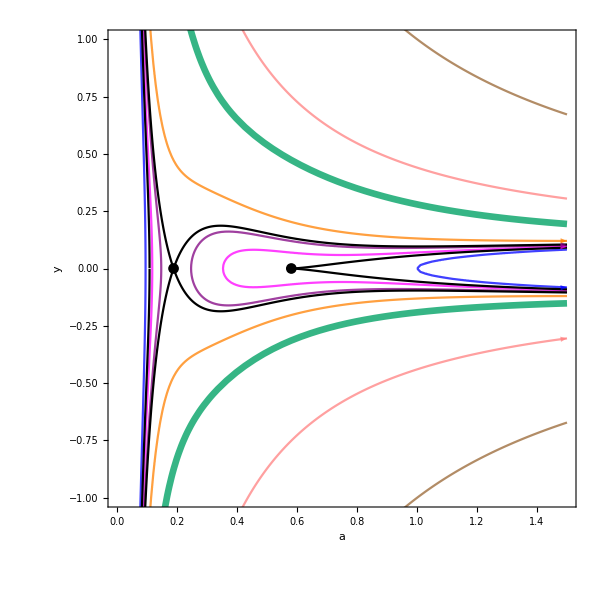

```mathematica
(*Show all components of plots*)
PhaseSpacec2=Show[Trajc2,FFSc2,CFSc2,Einsteinc2,PlotRange->{-1,1},FrameLabel->{"a",Rotate["y",270Degree]},AspectRatio->1,ImageSize->{600,600},BaseStyle->{FontSize->14}]
```

### Potential

```mathematica
(*Plot the potential for this case*)
Uc2=Plot[{U[a,0.1][[2]]},{a,0,1.5},AxesLabel->{"x","U"},PlotStyle->{Black}];
```

```mathematica
c2Energy[1]=Plot[{Energy[0.1,0][[2]]},{a,0,0.09},AxesLabel->{"x","U"},PlotStyle->{Blue,Opacity[0.75]}];
```

```mathematica
c2Energy[2]=Plot[{Energy[0.1,0][[2]]},{a,1,3},AxesLabel->{"x","U"},PlotStyle->{Blue,Opacity[0.75]}];
```

```mathematica
c2Energy[3]=Plot[{Energy[0.1,0.07][[2]]},{a,0,0.12},AxesLabel->{"x","U"},PlotStyle->{Magenta,Opacity[0.75]}];
```

```mathematica
c2Energy[4]=Plot[{Energy[0.1,0.07][[2]]},{a,0.355,3},AxesLabel->{"x","U"},PlotStyle->{Magenta,Opacity[0.75]}];
```

```mathematica
c2Energy[5]=Plot[{Energy[0.1,0.09][[2]]},{a,0,0.145},AxesLabel->{"x","U"},PlotStyle->{Purple,Opacity[0.75]}];
```

```mathematica
c2Energy[6]=Plot[{Energy[0.1,0.09][[2]]},{a,0.245,3},AxesLabel->{"x","U"},PlotStyle->{Purple,Opacity[0.75]}];
```

```mathematica
c2Energy[7]=Plot[{Energy[0.1,0.131][[2]]},{a,0.05,1},AxesLabel->{"x","U"},PlotStyle->{Orange,Opacity[0.75]}];
```

```mathematica
c2Energy[8]=Plot[{Energy[0.1,0.44][[2]]},{a,0.2,1},AxesLabel->{"x","U"},PlotStyle->{Pink,Opacity[0.75]}];
```

```mathematica
c2Energy[9]=Plot[{Energy[0.1,1][[2]]},{a,0.05,1},AxesLabel->{"x","U"},PlotStyle->{Brown,Opacity[0.75]}];
```

```mathematica
(*Energy of a trajectory that follows the FFS*)
c2Energy[10]=Plot[{0},{a,0.05,1},AxesLabel->{"x","U"},PlotStyle->{RGBColor[0.21,0.71,0.52],Thickness[0.008]}];
```

```mathematica
(*Plot dashed black lines between trajectories of the same energy*)
```

```mathematica
c2Energy[11]=Plot[{Energy[0.1,0][[2]]},{a,0.09,1},AxesLabel->{"x","U"},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
c2Energy[12]=Plot[{Energy[0.1,0.07][[2]]},{a,0.12,0.355},AxesLabel->{"x","U"},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
c2Energy[13]=Plot[{Energy[0.1,0.09][[2]]},{a,0.145,0.245},AxesLabel->{"x","U"},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
(*Add energies into a table*)
Energyc2=Table[c2Energy[i],{i,1,13}];
```

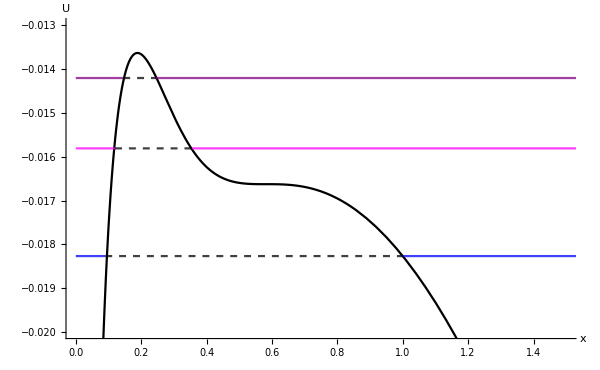

```mathematica
(*Show the potential and energy of the trajectories together*)
Potentialc2=Show[Uc2,Energyc2,ImageSize->{600,400},BaseStyle->{FontSize->14},PlotRange->{{0,1.5},{-0.02,-0.013}}]
```

### Final Plot

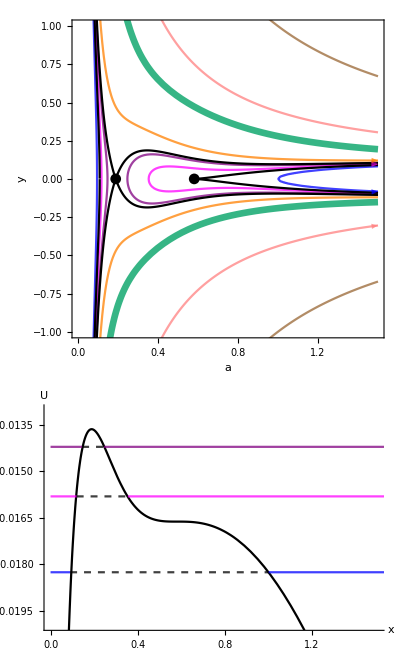

```mathematica
(*Plot the phase space and potential together*)
ayc2=GraphicsColumn[{PhaseSpacec2,Potentialc2},Spacings->{0,-20}]
```

```mathematica
(*Export["G:\\My Drive\\Wolfram Mathematica\\Project 1\\Non_Interacting_Matter\\Compact_Variables\\Full_Case\\x_Y_Z_R0.05\\Figures\\ay_Plots\\ayc2.pdf",ayc2]*)
```

## Three Einstein Points: c3

### Phase Space

```mathematica
(*Trajectories for the phase space*)
trajc3[y0_,x0_]:=y^2==x[a,x0]/3+z[a,x0,c[[3]]]/3+v[a,x0,cv]/3-(1/a^2)*(x[a0,x0]/3+z[a0,x0,c[[3]]]/3+v[a0,x0,cv]/3-y0^2);
```

```mathematica
c3traj[1]=ContourPlot[Evaluate[trajc3[0.071,0.08]],{a,0,aThreeEinsteinPointsc3[[1]]},{y,-1.5,1.5},PlotPoints->100,ContourStyle -> {{Blue, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c3traj[2]=ContourPlot[Evaluate[trajc3[0.071,0.08]],{a,aThreeEinsteinPointsc3[[1]],aThreeEinsteinPointsc3[[3]]},{y,-1.5,1.5},PlotPoints->200,ContourStyle -> {{Blue, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
c3traj[3]=ContourPlot[Evaluate[trajc3[0.071,0.08]],{a,aThreeEinsteinPointsc3[[3]],1.5},{y,-1.5,1.5},PlotPoints->100,ContourStyle -> {{Blue, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c3traj[4]=ContourPlot[Evaluate[trajc3[0.08,0.08]],{a,0,aThreeEinsteinPointsc3[[1]]},{y,-1.5,1.5},PlotPoints->100,ContourStyle -> {{Magenta,Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c3traj[5]=ContourPlot[Evaluate[trajc3[0.08,0.08]],{a,aThreeEinsteinPointsc3[[1]],1.5},{y,-1.5,1.5},PlotPoints->100,ContourStyle -> {{Magenta, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c3traj[6]=ContourPlot[Evaluate[trajc3[0.04,0.08]],{a,0,aThreeEinsteinPointsc3[[1]]},{y,-1.5,1.5},PlotPoints->100,ContourStyle -> {{Purple,Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c3traj[7]=ContourPlot[Evaluate[trajc3[0.04,0.08]],{a,aThreeEinsteinPointsc3[[3]],1.5},{y,-1.5,1.5},PlotPoints->100,ContourStyle -> {{Purple, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c3traj[8]=ContourPlot[Evaluate[trajc3[0.121,0.08]],{a,0,1.5},{y,0,1.5},PlotPoints->100,ContourStyle -> {{Orange, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c3traj[9]=ContourPlot[Evaluate[trajc3[0.121,0.08]],{a,0,1.5},{y,-1.5,0},PlotPoints->100,ContourStyle -> {{Orange, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c3traj[10]=ContourPlot[Evaluate[trajc3[0.31,0.08]],{a,0,1.5},{y,0,1.5},PlotPoints->100,ContourStyle -> {{Pink, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c3traj[11]=ContourPlot[Evaluate[trajc3[0.31,0.08]],{a,0,1.5},{y,-1.5,0},PlotPoints->100,ContourStyle -> {{Pink, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c3traj[12]=ContourPlot[Evaluate[trajc3[0.75,0.08]],{a,0,1.5},{y,0,1.5},PlotPoints->100,ContourStyle -> {{Brown, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c3traj[13]=ContourPlot[Evaluate[trajc3[0.75,0.08]],{a,0,1.5},{y,-1.5,0},PlotPoints->100,ContourStyle -> {{Brown, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
(*Add trajectories into a table*)
Trajc3=Table[c3traj[i],{i,1,13}];
```

```mathematica
(*Plot the FFS*)
(*Plot + and - FFS as a Sqrt was taken and Mathematica defaults to the + only*)
FFSc3=Plot[{FFS[a,0.08][[3]],-FFS[a,0.08][[3]]},{a,0,1.5},PlotStyle->{{RGBColor[0.21,0.71,0.52],Thickness[0.008]}},PlotRange->All];
```

```mathematica
(*Plot the CFS*)
(*Plot + and - CFS as a Sqrt was taken and Mathematica defaults to the + only*)
CFSc3=Plot[{CFS[a,aThreeEinsteinPointsc3,0.08][[3]],-CFS[a,aThreeEinsteinPointsc3,0.08][[3]]},{a,0,1.5},PlotStyle->{Black},PlotRange->All,PlotPoints->1000];
```

```mathematica
(*Plot the Einstein fixed points for this case*)
Einsteinc3=ListPlot[{{aThreeEinsteinPointsc3[[1]],0},{aThreeEinsteinPointsc3[[2]],0},{aThreeEinsteinPointsc3[[3]],0}},PlotStyle->{Black}];
```

```mathematica
(*Plot the accn = 0 curve for this case*)
Accnc3=ContourPlot[Accn[[3]]==0,{a,0,1.5},{y,-1.5,1.5},ContourStyle->{Red, Thick}];
```

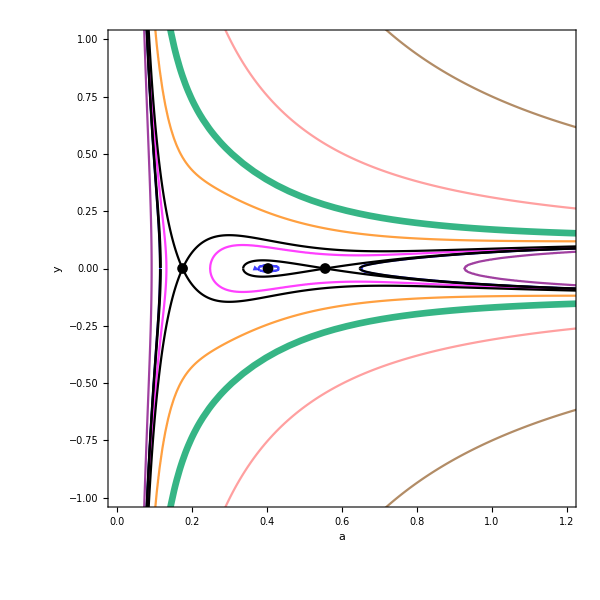

```mathematica
(*Show all components of plots*)
PhaseSpacec3=Show[Trajc3,FFSc3,CFSc3,Einsteinc3,PlotRange->{{0,1.2},{-1,1}},FrameLabel->{"a",Rotate["y",270Degree]},AspectRatio->1,ImageSize->{600,600},BaseStyle->{FontSize->14}]
```

### Potential

```mathematica
(*Plot the potential for this case*)
Uc3=Plot[{U[a,0.08][[3]]},{a,0,1.2},AxesLabel->{"x","U"},PlotStyle->{Black}];
```

```mathematica
c3Energy[1]=Plot[{Energy[0.08,0.071][[3]]},{a,0,0.115},AxesLabel->{"x","U"},PlotStyle->{Blue,Opacity[0.75]}];
```

```mathematica
c3Energy[2]=Plot[{Energy[0.08,0.071][[3]]},{a,0.37,0.43},AxesLabel->{"x","U"},PlotStyle->{Blue,Opacity[0.75]}];
```

```mathematica
c3Energy[3]=Plot[{Energy[0.08,0.071][[3]]},{a,0.64,3},AxesLabel->{"x","U"},PlotStyle->{Blue,Opacity[0.75]}];
```

```mathematica
c3Energy[4]=Plot[{Energy[0.08,0.08][[3]]},{a,0,0.13},AxesLabel->{"x","U"},PlotStyle->{Magenta,Opacity[0.75]}];
```

```mathematica
c3Energy[5]=Plot[{Energy[0.08,0.08][[3]]},{a,0.25,3},AxesLabel->{"x","U"},PlotStyle->{Magenta,Opacity[0.75]}];
```

```mathematica
c3Energy[6]=Plot[{Energy[0.08,0.04][[3]]},{a,0,0.09},AxesLabel->{"x","U"},PlotStyle->{Purple,Opacity[0.75]}];
```

```mathematica
c3Energy[7]=Plot[{Energy[0.08,0.04][[3]]},{a,0.925,3},AxesLabel->{"x","U"},PlotStyle->{Purple,Opacity[0.75]}];
```

```mathematica
c3Energy[8]=Plot[{Energy[0.08,0.121][[3]]},{a,0,3},AxesLabel->{"x","U"},PlotStyle->{Orange,Opacity[0.75]}];
```

```mathematica
c3Energy[9]=Plot[{Energy[0.08,0.31][[3]]},{a,0,3},AxesLabel->{"x","U"},PlotStyle->{Pink,Opacity[0.75]}];
```

```mathematica
c3Energy[10]=Plot[{Energy[0.08,0.75][[3]]},{a,0,3},AxesLabel->{"x","U"},PlotStyle->{Brown,Opacity[0.75]}];
```

```mathematica
(*Energy of a trajectory that follows the FFS*)
c3Energy[11]=Plot[{0},{a,0,3},AxesLabel->{"x","U"},PlotStyle->{RGBColor[0.21,0.71,0.52],Thickness[0.008]}];
```

```mathematica
(*Plot dashed black lines between trajectories of the same energy*)
```

```mathematica
c3Energy[12]=Plot[{Energy[0.08,0.071][[3]]},{a,0.115,0.37},AxesLabel->{"x","U"},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
c3Energy[13]=Plot[{Energy[0.08,0.071][[3]]},{a,0.43,0.64},AxesLabel->{"x","U"},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
c3Energy[14]=Plot[{Energy[0.08,0.08][[3]]},{a,0.13,0.25},AxesLabel->{"x","U"},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
c3Energy[15]=Plot[{Energy[0.08,0.04][[3]]},{a,0.09,0.925},AxesLabel->{"x","U"},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
(*Add energies into a table*)
Energyc3=Table[c3Energy[i],{i,1,15}];
```

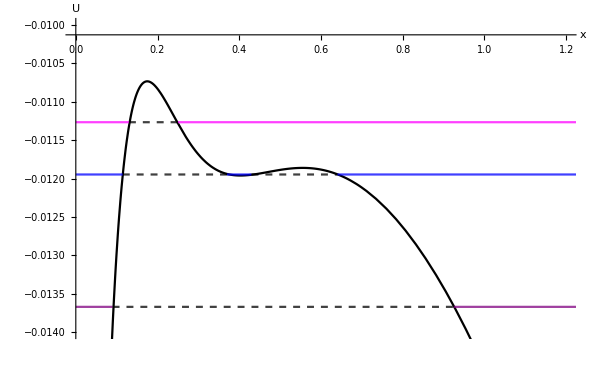

```mathematica
(*Show the potential and energy of the trajectories together*)
Potentialc3=Show[Uc3,Energyc3,ImageSize->{600,400},BaseStyle->{FontSize->14},PlotRange->{{0,1.2},{-0.014,-0.01}}]
```

### Final Plot

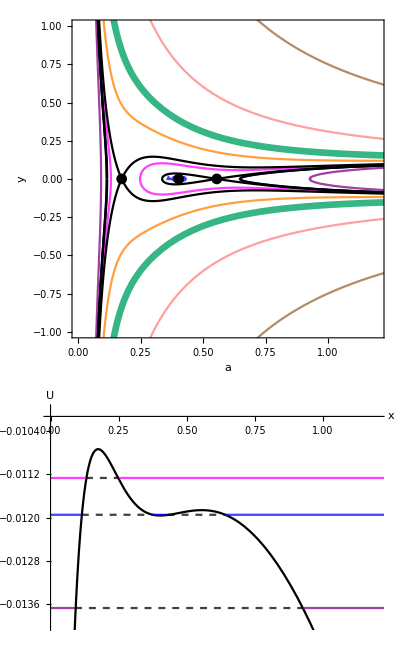

```mathematica
(*Plot the phase space and potential together*)
ayc3=GraphicsColumn[{PhaseSpacec3,Potentialc3},Spacings->{0,-20}]
```

```mathematica
(*Export["G:\\My Drive\\Wolfram Mathematica\\Project 1\\Non_Interacting_Matter\\Compact_Variables\\Full_Case\\x_Y_Z_R0.05\\Figures\\ay_Plots\\ayc3.pdf",ayc3]*)
```

## Three Einstein Points: c4

### Phase Space

```mathematica
(*Trajectories for the phase space*)
trajc4[y0_,x0_]:=y^2==x[a,x0]/3+z[a,x0,c[[4]]]/3+v[a,x0,cv]/3-(1/a^2)*(x[a0,x0]/3+z[a0,x0,c[[4]]]/3+v[a0,x0,cv]/3-y0^2);
```

```mathematica
c4traj[1]=ContourPlot[Evaluate[trajc4[0.065,0.08]],{a,0,aThreeEinsteinPointsc4[[1]]},{y,-1.5,1.5},PlotPoints->100,ContourStyle -> {{Blue, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,0,.02,.02,0,0},1]]],Arrow[x]};
```

```mathematica
c4traj[2]=ContourPlot[Evaluate[trajc4[0.065,0.08]],{a,aThreeEinsteinPointsc4[[1]],aThreeEinsteinPointsc4[[3]]},{y,-1.5,1.5},PlotPoints->100,ContourStyle -> {{Blue, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,0,.02,0,0,.02,0,0},1]]],Arrow[x]};
```

```mathematica
c4traj[3]=ContourPlot[Evaluate[trajc4[0.065,0.08]],{a,aThreeEinsteinPointsc4[[3]],1.5},{y,-1.5,1.5},PlotPoints->100,ContourStyle -> {{Blue, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c4traj[4]=ContourPlot[Evaluate[trajc4[0.05,0.08]],{a,0,aThreeEinsteinPointsc4[[1]]},{y,-1.5,1.5},PlotPoints->100,ContourStyle -> {{Magenta, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c4traj[5]=ContourPlot[Evaluate[trajc4[0.05,0.08]],{a,aThreeEinsteinPointsc4[[3]],1.5},{y,-1.5,1.5},PlotPoints->100,ContourStyle -> {{Magenta, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c4traj[6]=ContourPlot[Evaluate[trajc4[0.11,0.08]],{a,0,1.5},{y,-1.5,0},PlotPoints->100,ContourStyle -> {{Orange, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c4traj[7]=ContourPlot[Evaluate[trajc4[0.11,0.08]],{a,0,1.5},{y,0,1.5},PlotPoints->100,ContourStyle -> {{Orange, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c4traj[8]=ContourPlot[Evaluate[trajc4[0.31,0.08]],{a,0,1.5},{y,-1.5,0},PlotPoints->100,ContourStyle -> {{Pink, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c4traj[9]=ContourPlot[Evaluate[trajc4[0.31,0.08]],{a,0,1.5},{y,0,1.5},PlotPoints->100,ContourStyle -> {{Pink, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c4traj[10]=ContourPlot[Evaluate[trajc4[0.75,0.08]],{a,0,1.5},{y,-1.5,0},PlotPoints->100,ContourStyle -> {{Brown, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c4traj[11]=ContourPlot[Evaluate[trajc4[0.75,0.08]],{a,0,1.5},{y,0,1.5},PlotPoints->100,ContourStyle -> {{Brown, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
(*Add trajectories into a table*)
Trajc4=Table[c4traj[i],{i,1,11}];
```

```mathematica
(*Plot the FFS*)
(*Plot + and - FFS as a Sqrt was taken and Mathematica defaults to the + only*)
FFSc4=Plot[{FFS[a,0.08][[4]],-FFS[a,0.08][[4]]},{a,0,1.5},PlotStyle->{{RGBColor[0.21,0.71,0.52],Thickness[0.008]}},PlotRange->All];
```

```mathematica
(*Plot the CFS*)
(*Plot + and - CFS as a Sqrt was taken and Mathematica defaults to the + only*)
CFSc4=Plot[{CFS[a,aThreeEinsteinPointsc4,0.08][[4]],-CFS[a,aThreeEinsteinPointsc4,0.08][[4]]},{a,0,1.5},PlotStyle->{Black},PlotRange->All,PlotPoints->1000];
```

```mathematica
(*Plot the Einstein fixed points for this case*)
Einsteinc4=ListPlot[{{aThreeEinsteinPointsc4[[1]],0},{aThreeEinsteinPointsc4[[2]],0},{aThreeEinsteinPointsc4[[3]],0}},PlotStyle->{Black}];
```

```mathematica
(*Plot the accn = 0 curve for this case*)
Accnc4=ContourPlot[Accn[[4]]==0,{a,0,1.5},{y,-1.5,1.5},ContourStyle->{Red, Thick}];
```

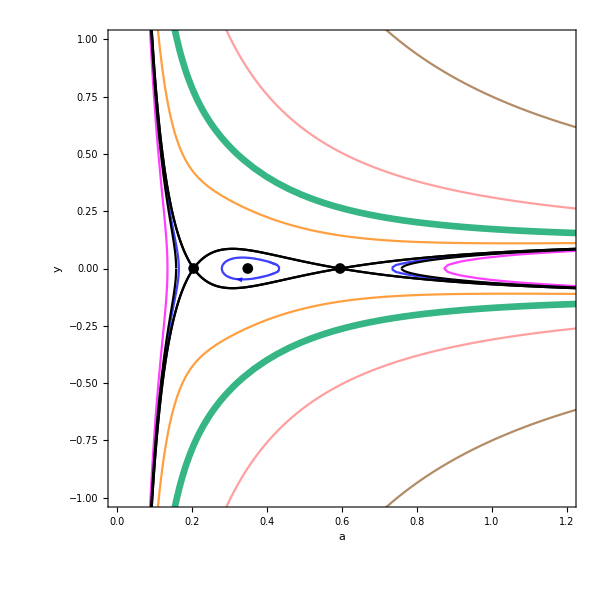

```mathematica
(*Show all components of plots*)
PhaseSpacec4=Show[Trajc4,FFSc4,CFSc4,Einsteinc4,PlotRange->{{0,1.2},{-1,1}},FrameLabel->{"a",Rotate["y",270Degree]},AspectRatio->1,ImageSize->{600,600},BaseStyle->{FontSize->14}]
```

### Potential

```mathematica
(*Plot the potential for this case*)
Uc4=Plot[{U[a,0.08][[4]]},{a,0,1.2},AxesLabel->{"x","U"},PlotStyle->{Black}];
```

```mathematica
c4Energy[1]=Plot[{Energy[0.08,0.065][[4]]},{a,0,0.16},AxesLabel->{"x","U"},PlotStyle->{Blue,Opacity[0.75]}];
```

```mathematica
c4Energy[2]=Plot[{Energy[0.08,0.065][[4]]},{a,0.28,0.435},AxesLabel->{"x","U"},PlotStyle->{Blue,Opacity[0.75]}];
```

```mathematica
c4Energy[3]=Plot[{Energy[0.08,0.065][[4]]},{a,0.73,3},AxesLabel->{"x","U"},PlotStyle->{Blue,Opacity[0.75]}];
```

```mathematica
c4Energy[4]=Plot[{Energy[0.08,0.05][[4]]},{a,0,0.135},AxesLabel->{"x","U"},PlotStyle->{Magenta,Opacity[0.75]}];
```

```mathematica
c4Energy[5]=Plot[{Energy[0.08,0.05][[4]]},{a,0.87,3},AxesLabel->{"x","U"},PlotStyle->{Magenta,Opacity[0.75]}];
```

```mathematica
c4Energy[6]=Plot[{Energy[0.08,0.11][[4]]},{a,0,3},AxesLabel->{"x","U"},PlotStyle->{Orange,Opacity[0.75]}];
```

```mathematica
c4Energy[7]=Plot[{Energy[0.08,0.31][[4]]},{a,0,3},AxesLabel->{"x","U"},PlotStyle->{Pink,Opacity[0.75]}];
```

```mathematica
c4Energy[8]=Plot[{Energy[0.08,0.75][[4]]},{a,0,3},AxesLabel->{"x","U"},PlotStyle->{Brown,Opacity[0.75]}];
```

```mathematica
(*Energy of a trajectory that follows the FFS*)
c4Energy[9]=Plot[{0},{a,0,3},AxesLabel->{"x","U"},PlotStyle->{RGBColor[0.21,0.71,0.52],Thickness[0.008]}];
```

```mathematica
(*Plot dashed black lines between trajectories of the same energy*)
```

```mathematica
c4Energy[10]=Plot[{Energy[0.08,0.065][[4]]},{a,0.16,0.28},AxesLabel->{"x","U"},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
c4Energy[11]=Plot[{Energy[0.08,0.065][[4]]},{a,0.435,0.73},AxesLabel->{"x","U"},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
c4Energy[12]=Plot[{Energy[0.08,0.05][[4]]},{a,0.135,0.87},AxesLabel->{"x","U"},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
(*Add energies into a table*)
Energyc4=Table[c4Energy[i],{i,1,12}];
```

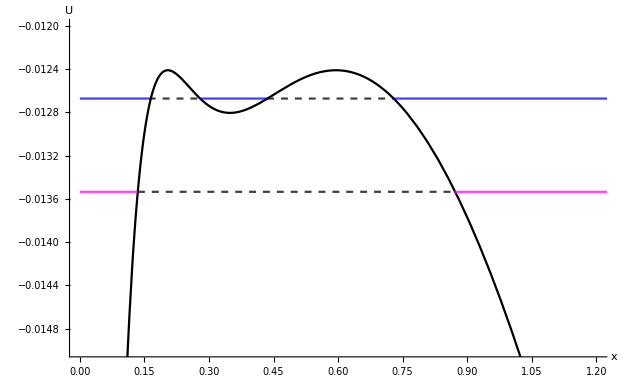

```mathematica
(*Show the potential and energy of the trajectories together*)
Potentialc4=Show[Uc4,Energyc4,ImageSize->{600,400},BaseStyle->{FontSize->14},PlotRange->{{0,1.2},{-0.015,-0.012}}]
```

### Final Plot

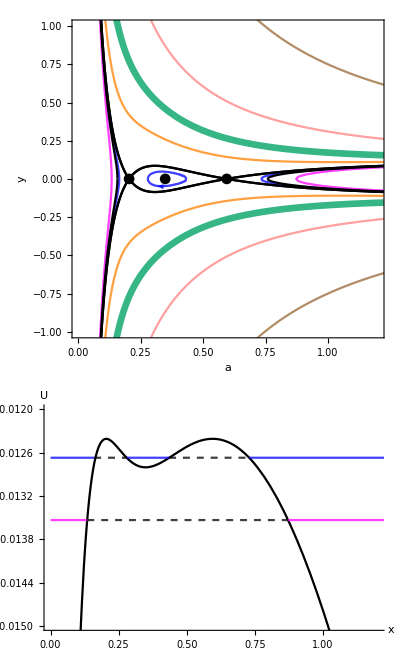

```mathematica
(*Plot the phase space and potential together*)
ayc4=GraphicsColumn[{PhaseSpacec4,Potentialc4},Spacings->{0,-20}]
```

```mathematica
(*Export["G:\\My Drive\\Wolfram Mathematica\\Project 1\\Non_Interacting_Matter\\Compact_Variables\\Full_Case\\x_Y_Z_R0.05\\Figures\\ay_Plots\\ayc4.pdf",ayc4]*)
```

## Three Einstein Points: c5

### Phase Space

```mathematica
(*Trajectories for the phase space*)
trajc5[y0_,x0_]:=y^2==x[a,x0]/3+z[a,x0,c[[5]]]/3+v[a,x0,cv]/3-(1/a^2)*(x[a0,x0]/3+z[a0,x0,c[[5]]]/3+v[a0,x0,cv]/3-y0^2);
```

```mathematica
c5traj[1]=ContourPlot[Evaluate[trajc5[0.06,0.08]],{a,0,aThreeEinsteinPointsc5[[1]]},{y,-1.5,1.5},PlotPoints->100,ContourStyle -> {{Blue, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c5traj[2]=ContourPlot[Evaluate[trajc5[0.06,0.08]],{a,aThreeEinsteinPointsc5[[1]],aThreeEinsteinPointsc5[[3]]},{y,-1.5,1.5},PlotPoints->150,ContourStyle -> {{Blue, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0,0,-.02,0},1]]],Arrow[x]};
```

```mathematica
c5traj[3]=ContourPlot[Evaluate[trajc5[0.06,0.08]],{a,aThreeEinsteinPointsc5[[3]],1.5},{y,-1.5,1.5},PlotPoints->100,ContourStyle -> {{Blue, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c5traj[4]=ContourPlot[Evaluate[trajc5[0.065,0.08]],{a,0,aThreeEinsteinPointsc5[[3]]},{y,-1.5,1.5},PlotPoints->100,ContourStyle -> {{Magenta, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c5traj[5]=ContourPlot[Evaluate[trajc5[0.065,0.08]],{a,aThreeEinsteinPointsc5[[3]],1.5},{y,-1.5,1.5},PlotPoints->100,ContourStyle -> {{Magenta, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c5traj[6]=ContourPlot[Evaluate[trajc5[0.05,0.08]],{a,0,aThreeEinsteinPointsc5[[1]]},{y,-1.5,1.5},PlotPoints->100,ContourStyle -> {{Purple, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c5traj[7]=ContourPlot[Evaluate[trajc5[0.05,0.08]],{a,aThreeEinsteinPointsc5[[3]],1.5},{y,-1.5,1.5},PlotPoints->100,ContourStyle -> {{Purple, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c5traj[8]=ContourPlot[Evaluate[trajc5[0.11,0.08]],{a,0,1.5},{y,-1.5,0},PlotPoints->100,ContourStyle -> {{Orange, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c5traj[9]=ContourPlot[Evaluate[trajc5[0.11,0.08]],{a,0,1.5},{y,0,1.5},PlotPoints->100,ContourStyle -> {{Orange, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c5traj[10]=ContourPlot[Evaluate[trajc5[0.31,0.08]],{a,0,1.5},{y,-1.5,0},PlotPoints->100,ContourStyle -> {{Pink, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c5traj[11]=ContourPlot[Evaluate[trajc5[0.31,0.08]],{a,0,1.5},{y,0,1.5},PlotPoints->100,ContourStyle -> {{Pink, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c5traj[12]=ContourPlot[Evaluate[trajc5[0.75,0.08]],{a,0,1.5},{y,-1.5,0},PlotPoints->100,ContourStyle -> {{Brown, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c5traj[13]=ContourPlot[Evaluate[trajc5[0.75,0.08]],{a,0,1.5},{y,0,1.5},PlotPoints->100,ContourStyle -> {{Brown, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
(*Add trajectories into a table*)
Trajc5=Table[c5traj[i],{i,1,13}];
```

```mathematica
(*Plot the FFS*)
(*Plot + and - FFS as a Sqrt was taken and Mathematica defaults to the + only*)
FFSc5=Plot[{FFS[a,0.08][[5]],-FFS[a,0.08][[5]]},{a,0,1.5},PlotStyle->{{RGBColor[0.21,0.71,0.52],Thickness[0.008]}},PlotRange->All];
```

```mathematica
(*Plot the CFS*)
(*Plot + and - CFS as a Sqrt was taken and Mathematica defaults to the + only*)
CFSc5=Plot[{CFS[a,aThreeEinsteinPointsc5,0.08][[5]],-CFS[a,aThreeEinsteinPointsc5,0.08][[5]]},{a,0,1.5},PlotStyle->{Black},PlotRange->All,PlotPoints->1000];
```

```mathematica
(*Plot the Einstein fixed points for this case*)
Einsteinc5=ListPlot[{{aThreeEinsteinPointsc5[[1]],0},{aThreeEinsteinPointsc5[[2]],0},{aThreeEinsteinPointsc5[[3]],0}},PlotStyle->{Black}];
```

```mathematica
(*Plot the accn = 0 curve for this case*)
Accnc5=ContourPlot[Accn[[5]]==0,{a,0,1.5},{y,-1.5,1.5},ContourStyle->{Red, Thick}];
```

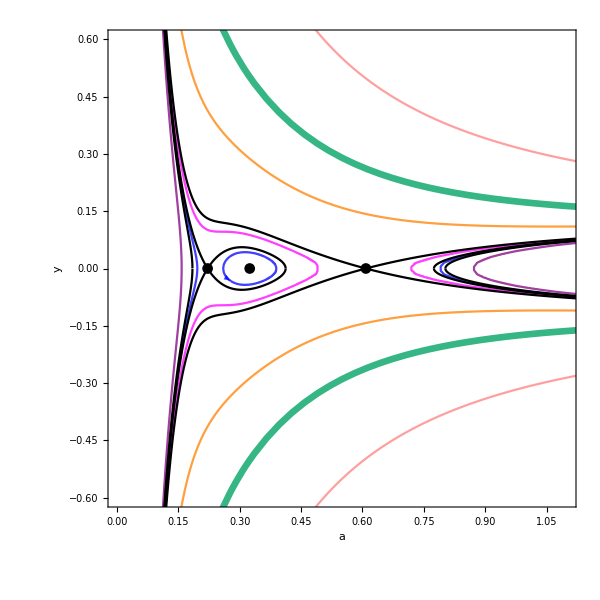

```mathematica
(*Show all components of plots*)
PhaseSpacec5=Show[Trajc5,FFSc5,CFSc5,Einsteinc5,PlotRange->{{0,1.1},{-0.6,0.6}},FrameLabel->{"a",Rotate["y",270Degree]},AspectRatio->1,ImageSize->{600,600},BaseStyle->{FontSize->14}]
```

### Potential

```mathematica
(*Plot the potential for this case*)
Uc5=Plot[{U[a,0.08][[5]]},{a,0,1.1},AxesLabel->{"x","U"},PlotStyle->{Black}];
```

```mathematica
c5Energy[1]=Plot[{Energy[0.08,0.06][[5]]},{a,0,0.195},AxesLabel->{"x","U"},PlotStyle->{Blue,Opacity[0.75]}];
```

```mathematica
c5Energy[2]=Plot[{Energy[0.08,0.06][[5]]},{a,0.26,0.39},AxesLabel->{"x","U"},PlotStyle->{Blue,Opacity[0.75]}];
```

```mathematica
c5Energy[3]=Plot[{Energy[0.08,0.06][[5]]},{a,0.785,3},AxesLabel->{"x","U"},PlotStyle->{Blue,Opacity[0.75]}];
```

```mathematica
c5Energy[4]=Plot[{Energy[0.08,0.065][[5]]},{a,0,0.495},AxesLabel->{"x","U"},PlotStyle->{Magenta,Opacity[0.75]}];
```

```mathematica
c5Energy[5]=Plot[{Energy[0.08,0.065][[5]]},{a,0.715,3},AxesLabel->{"x","U"},PlotStyle->{Magenta,Opacity[0.75]}];
```

```mathematica
c5Energy[6]=Plot[{Energy[0.08,0.05][[5]]},{a,0,0.16},AxesLabel->{"x","U"},PlotStyle->{Purple,Opacity[0.75]}];
```

```mathematica
c5Energy[7]=Plot[{Energy[0.08,0.05][[5]]},{a,0.87,3},AxesLabel->{"x","U"},PlotStyle->{Purple,Opacity[0.75]}];
```

```mathematica
c5Energy[8]=Plot[{Energy[0.08,0.11][[5]]},{a,0,3},AxesLabel->{"x","U"},PlotStyle->{Orange,Opacity[0.75]}];
```

```mathematica
c5Energy[9]=Plot[{Energy[0.08,0.31][[5]]},{a,0,3},AxesLabel->{"x","U"},PlotStyle->{Pink,Opacity[0.75]}];
```

```mathematica
c5Energy[10]=Plot[{Energy[0.08,0.75][[5]]},{a,0,3},AxesLabel->{"x","U"},PlotStyle->{Brown,Opacity[0.75]}];
```

```mathematica
(*Energy of a trajectory that follows the FFS*)
c5Energy[11]=Plot[{0},{a,0,3},AxesLabel->{"x","U"},PlotStyle->{RGBColor[0.21,0.71,0.52],Thickness[0.008]}];
```

```mathematica
(*Plot dashed black lines between trajectories of the same energy*)
```

```mathematica
c5Energy[12]=Plot[{Energy[0.08,0.06][[5]]},{a,0.195,0.26},AxesLabel->{"x","U"},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
c5Energy[13]=Plot[{Energy[0.08,0.06][[5]]},{a,0.39,0.785},AxesLabel->{"x","U"},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
c5Energy[14]=Plot[{Energy[0.08,0.065][[5]]},{a,0.495,0.715},AxesLabel->{"x","U"},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
c5Energy[15]=Plot[{Energy[0.08,0.05][[5]]},{a,0.16,0.87},AxesLabel->{"x","U"},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
(*Add energies into a table*)
Energyc5=Table[c5Energy[i],{i,1,15}];
```

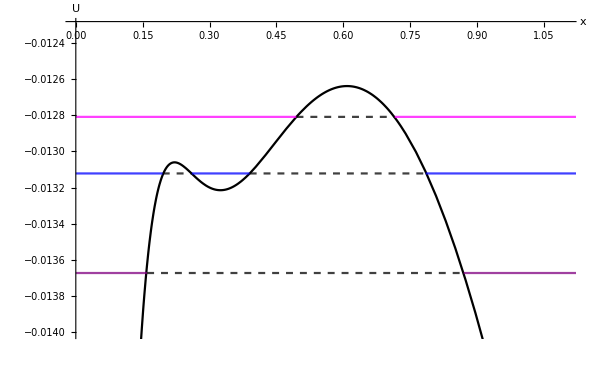

```mathematica
(*Show the potential and energy of the trajectories together*)
Potentialc5=Show[Uc5,Energyc5,ImageSize->{600,400},BaseStyle->{FontSize->14},PlotRange->{{0,1.1},{-0.014,-0.0123}}]
```

### Final Plot

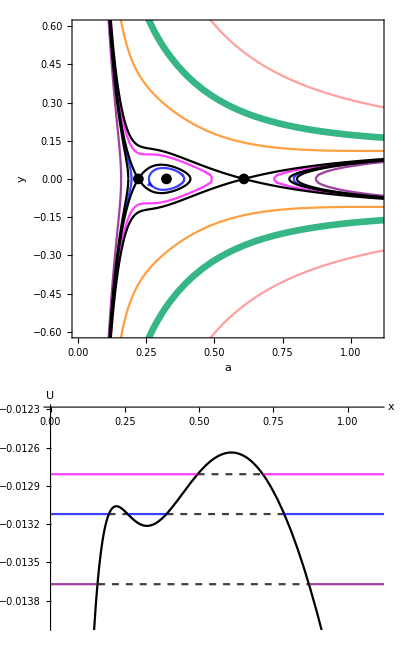

```mathematica
(*Plot the phase space and potential together*)
ayc5=GraphicsColumn[{PhaseSpacec5,Potentialc5},Spacings->{0,-20}]
```

```mathematica
(*Export["G:\\My Drive\\Wolfram Mathematica\\Project 1\\Non_Interacting_Matter\\Compact_Variables\\Full_Case\\x_Y_Z_R0.05\\Figures\\ay_Plots\\ayc5.pdf",ayc5]*)
```

## Two Einstein Points: c6

### Phase Space

```mathematica
(*Trajectories for the phase space*)
trajc6[y0_,x0_]:=y^2==x[a,x0]/3+z[a,x0,c[[6]]]/3+v[a,x0,cv]/3-(1/a^2)*(x[a0,x0]/3+z[a0,x0,c[[6]]]/3+v[a0,x0,cv]/3-y0^2);
```

```mathematica
c6traj[1]=ContourPlot[Evaluate[trajc6[0,0.9]],{a,0,aTwoEinsteinPointsc6[[1]]},{y,-1.5,1.5},PlotPoints->100,ContourStyle -> {{Blue, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c6traj[2]=ContourPlot[Evaluate[trajc6[0,0.9]],{a,aTwoEinsteinPointsc6[[2]],10},{y,-1.5,1.5},PlotPoints->100,ContourStyle -> {{Blue,Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c6traj[3]=ContourPlot[Evaluate[trajc6[0.44,0.9]],{a,0,aTwoEinsteinPointsc6[[2]]},{y,-1.5,1.5},PlotPoints->100,ContourStyle -> {{Magenta, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c6traj[4]=ContourPlot[Evaluate[trajc6[0.44,0.9]],{a,aTwoEinsteinPointsc6[[2]],10},{y,-1.5,1.5},PlotPoints->100,ContourStyle -> {{Magenta, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c6traj[5]=ContourPlot[Evaluate[trajc6[0.75,0.9]],{a,0,10},{y,0,1.5},PlotPoints->100,ContourStyle -> {{Orange, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c6traj[6]=ContourPlot[Evaluate[trajc6[0.75,0.9]],{a,0,10},{y,-1.5,0},PlotPoints->100,ContourStyle -> {{Orange, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c6traj[7]=ContourPlot[Evaluate[trajc6[2.06,0.9]],{a,0,10},{y,-1.5,0},PlotPoints->100,ContourStyle -> {{Pink, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c6traj[8]=ContourPlot[Evaluate[trajc6[2.06,0.9]],{a,0,10},{y,0,1.5},PlotPoints->100,ContourStyle -> {{Pink, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c6traj[9]=ContourPlot[Evaluate[trajc6[7.02,0.9]],{a,0,10},{y,0,1.5},PlotPoints->100,ContourStyle -> {{Brown, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c6traj[10]=ContourPlot[Evaluate[trajc6[7.02,0.9]],{a,0,10},{y,-1.5,0},PlotPoints->100,ContourStyle -> {{Brown, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
(*Add trajectories into a table*)
Trajc6=Table[c6traj[i],{i,1,10}];
```

```mathematica
(*Plot the FFS*)
(*Plot + and - FFS as a Sqrt was taken and Mathematica defaults to the + only*)
FFSc6=Plot[{FFS[a,0.9][[6]],-FFS[a,0.9][[6]]},{a,0,10},PlotStyle->{{RGBColor[0.21,0.71,0.52],Thickness[0.008]}},PlotRange->All];
```

```mathematica
(*Plot the CFS*)
(*Plot + and - CFS as a Sqrt was taken and Mathematica defaults to the + only*)
CFSc6=Plot[{CFS[a,aTwoEinsteinPointsc6,0.9][[6]],-CFS[a,aTwoEinsteinPointsc6,0.9][[6]]},{a,0.1,10},PlotStyle->{Black},PlotRange->All,PlotPoints->100];
```

```mathematica
(*Plot the Einstein fixed points for this case*)
Einsteinc6=ListPlot[{{aTwoEinsteinPointsc6[[1]],0},{aTwoEinsteinPointsc6[[2]],0}},PlotStyle->{Black}];
```

```mathematica
(*Plot the accn = 0 curve for this case*)
Accnc6=ContourPlot[Accn[[6]]==0,{a,0,10},{y,-1.5,1.5},ContourStyle->{Red, Thick}];
```

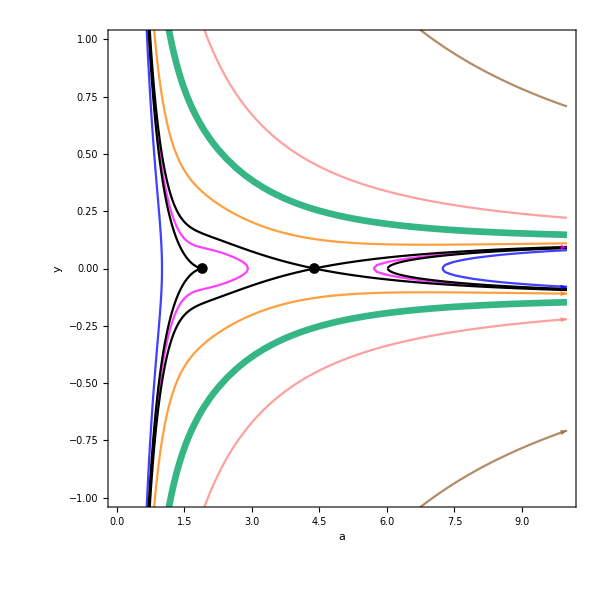

```mathematica
(*Show all components of plots*)
PhaseSpacec6=Show[Trajc6,FFSc6,CFSc6,Einsteinc6,PlotRange->{-1,1},FrameLabel->{"a",Rotate["y",270Degree]},AspectRatio->1,ImageSize->{600,600},BaseStyle->{FontSize->14}]
```

### Potential

```mathematica
(*Plot the potential for this case*)
Uc6=Plot[{U[a,0.9][[6]]},{a,0,10},AxesLabel->{"x","U"},PlotStyle->{Black}];
```

```mathematica
c6Energy[1]=Plot[{Energy[0.9,0][[6]]},{a,0,1},AxesLabel->{"x","U"},PlotStyle->{Blue,Opacity[0.75]}];
```

```mathematica
c6Energy[2]=Plot[{Energy[0.9,0][[6]]},{a,7.2,10},AxesLabel->{"x","U"},PlotStyle->{Blue,Opacity[0.75]}];
```

```mathematica
c6Energy[3]=Plot[{Energy[0.9,0.44][[6]]},{a,0,2.95},AxesLabel->{"x","U"},PlotStyle->{Magenta,Opacity[0.75]}];
```

```mathematica
c6Energy[4]=Plot[{Energy[0.9,0.44][[6]]},{a,5.65,10},AxesLabel->{"x","U"},PlotStyle->{Magenta,Opacity[0.75]}];
```

```mathematica
c6Energy[5]=Plot[{Energy[0.9,0.75][[6]]},{a,0,10},AxesLabel->{"x","U"},PlotStyle->{Orange,Opacity[0.75]}];
```

```mathematica
c6Energy[6]=Plot[{Energy[0.9,2.06][[6]]},{a,0,10},AxesLabel->{"x","U"},PlotStyle->{Pink,Dashed,Opacity[0.75]}];
```

```mathematica
c6Energy[7]=Plot[{Energy[0.9,7.02][[6]]},{a,0,10},AxesLabel->{"x","U"},PlotStyle->{Brown,Opacity[0.75]}];
```

```mathematica
(*Energy of a trajectory that follows the FFS*)
c6Energy[8]=Plot[{0},{a,0,10},AxesLabel->{"x","U"},PlotStyle->{RGBColor[0.21,0.71,0.52],Thickness[0.008]}];
```

```mathematica
(*Plot dashed black lines between trajectories of the same energy*)
```

```mathematica
c6Energy[9]=Plot[{Energy[0.9,0][[6]]},{a,1,7.2},AxesLabel->{"x","U"},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
c6Energy[10]=Plot[{Energy[0.9,0.44][[6]]},{a,2.95,5.65},AxesLabel->{"x","U"},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
(*Add energies into a table*)
Energyc6=Table[c6Energy[i],{i,1,10}];
```

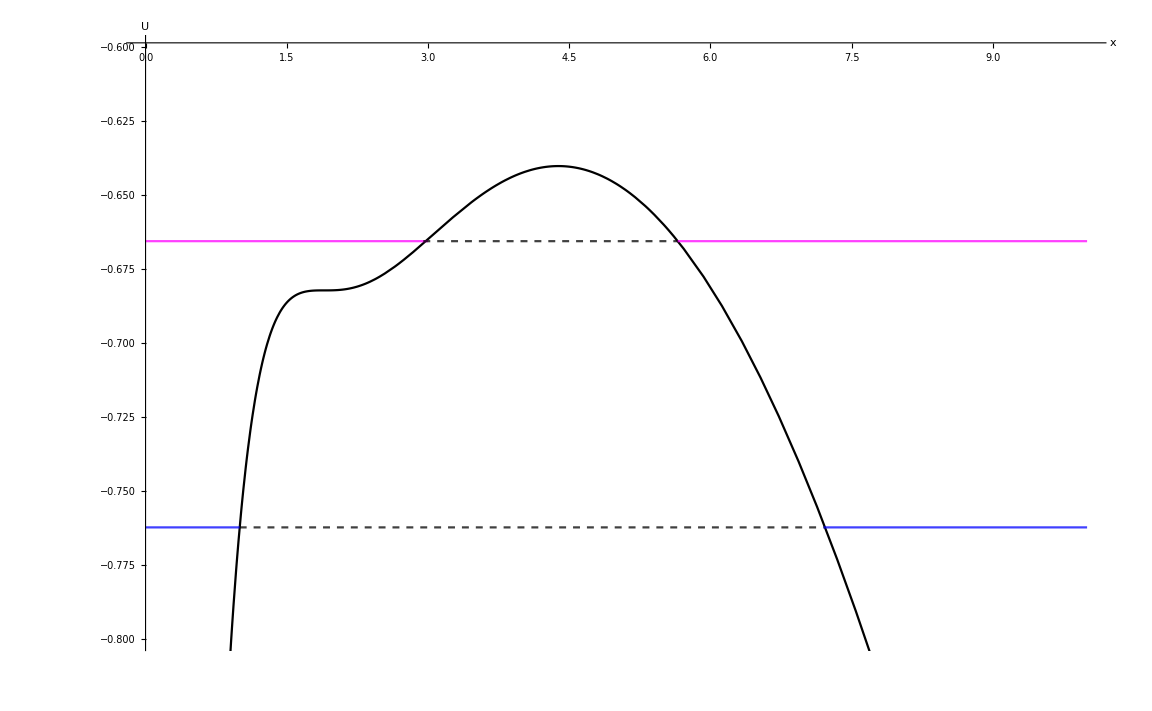

```mathematica
(*Show the potential and energy of the trajectories together*)
Potentialc6=Show[Uc6,Energyc6,ImageSize->{600,400},BaseStyle->{FontSize->14},PlotRange->{-0.8,-0.6}]
```

### Final Plot

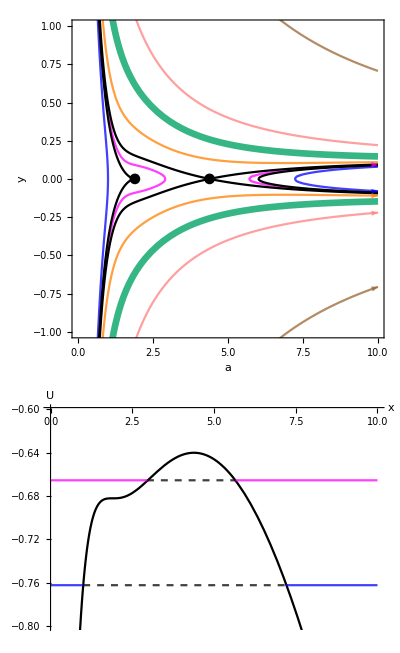

```mathematica
(*Plot the phase space and potential together*)
ayc6=GraphicsColumn[{PhaseSpacec6,Potentialc6},Spacings->{0,-20}]
```

```mathematica
(*Export["G:\\My Drive\\Wolfram Mathematica\\Project 1\\Non_Interacting_Matter\\Compact_Variables\\Full_Case\\x_Y_Z_R0.05\\Figures\\ay_Plots\\ayc6.pdf",ayc6]*)
```

## One Einstein Point: c7

### Phase Space

```mathematica
(*Trajectories for the phase space*)
trajc7[y0_,x0_]:=y^2==x[a,x0]/3+z[a,x0,c[[7]]]/3+v[a,x0,cv]/3-(1/a^2)*(x[a0,x0]/3+z[a0,x0,c[[7]]]/3+v[a0,x0,cv]/3-y0^2);
```

```mathematica
c7traj[1]=ContourPlot[Evaluate[trajc7[0,0.9]],{a,0,aOneEinsteinPointc7},{y,-1.5,1.5},PlotPoints->100,ContourStyle -> {{Blue, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c7traj[2]=ContourPlot[Evaluate[trajc7[0,0.9]],{a,aOneEinsteinPointc7,10},{y,-1.5,1.5},PlotPoints->100,ContourStyle -> {{Blue, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c7traj[3]=ContourPlot[Evaluate[trajc7[0.58,0.9]],{a,0,aOneEinsteinPointc7},{y,-1.5,1.5},PlotPoints->100,ContourStyle -> {{Magenta, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c7traj[4]=ContourPlot[Evaluate[trajc7[0.58,0.9]],{a,aOneEinsteinPointc7,10},{y,-1.5,1.5},PlotPoints->100,ContourStyle -> {{Magenta, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c7traj[5]=ContourPlot[Evaluate[trajc7[0.68,0.9]],{a,0,aOneEinsteinPointc7},{y,-1.5,1.5},PlotPoints->100,ContourStyle -> {{Purple, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c7traj[6]=ContourPlot[Evaluate[trajc7[0.68,0.9]],{a,aOneEinsteinPointc7,10},{y,-1.5,1.5},PlotPoints->100,ContourStyle -> {{Purple, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c7traj[7]=ContourPlot[Evaluate[trajc7[0.98,0.9]],{a,0,10},{y,0,1.5},PlotPoints->100,ContourStyle -> {{Orange, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c7traj[8]=ContourPlot[Evaluate[trajc7[0.98,0.9]],{a,0,10},{y,-1.5,0},PlotPoints->100,ContourStyle -> {{Orange, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c7traj[9]=ContourPlot[Evaluate[trajc7[2.35,0.9]],{a,0,10},{y,0,1.5},PlotPoints->100,ContourStyle -> {{Pink, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c7traj[10]=ContourPlot[Evaluate[trajc7[2.35,0.9]],{a,0,10},{y,-1.5,0},PlotPoints->100,ContourStyle -> {{Pink, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c7traj[11]=ContourPlot[Evaluate[trajc7[7.02,0.9]],{a,0,10},{y,0,1.5},PlotPoints->100,ContourStyle -> {{Brown, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c7traj[12]=ContourPlot[Evaluate[trajc7[7.02,0.9]],{a,0,10},{y,-1.5,0},PlotPoints->100,ContourStyle -> {{Brown, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
(*Add trajectories into a table*)
Trajc7=Table[c7traj[i],{i,1,12}];
```

```mathematica
(*Plot the FFS*)
(*Plot + and - FFS as a Sqrt was taken and Mathematica defaults to the + only*)
FFSc7=Plot[{FFS[a,0.9][[7]],-FFS[a,0.9][[7]]},{a,0,10},PlotStyle->{{RGBColor[0.21,0.71,0.52],Thickness[0.008]}},PlotRange->All];
```

```mathematica
(*Plot the CFS*)
(*Plot + and - CFS as a Sqrt was taken and Mathematica defaults to the + only*)
CFSc7=Plot[{CFS[a,aOneEinsteinPointc7,0.9][[7]],-CFS[a,aOneEinsteinPointc7,0.9][[7]]},{a,0,10},PlotStyle->{Black},PlotRange->All];
```

```mathematica
(*Plot the Einstein fixed points for this case*)
Einsteinc7=ListPlot[{{aOneEinsteinPointc7,0}},PlotStyle->{Black}];
```

```mathematica
(*Plot the accn = 0 curve for this case*)
Accnc7=ContourPlot[Accn[[7]]==0,{a,0,3},{y,-1.5,1.5},ContourStyle->{Red, Thick}];
```

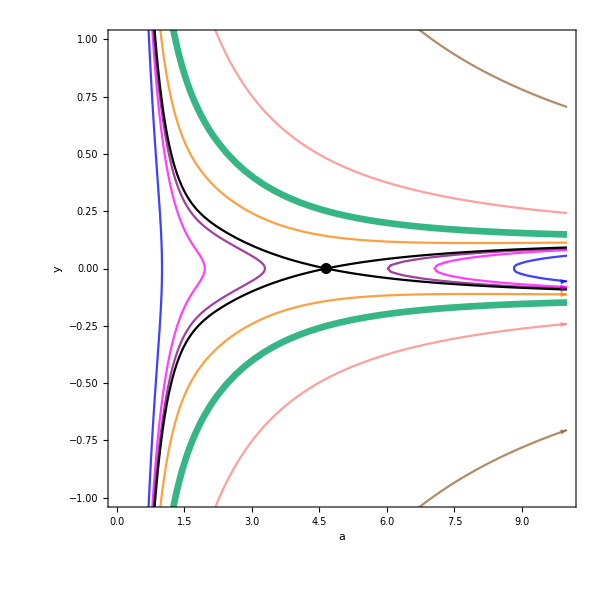

```mathematica
(*Show all components of plots*)
PhaseSpacec7=Show[Trajc7,FFSc7,CFSc7,Einsteinc7,PlotRange->{-1,1},FrameLabel->{"a",Rotate["y",270Degree]},AspectRatio->1,ImageSize->{600,600},BaseStyle->{FontSize->14}]
```

### Potential

```mathematica
(*Plot the potential for this case*)
Uc7=Plot[{U[a,0.9][[7]]},{a,0,10},AxesLabel->{"x","U"},PlotStyle->{Black}];
```

```mathematica
c7Energy[1]=Plot[{Energy[0.9,0][[7]]},{a,0,1},AxesLabel->{"x","U"},PlotStyle->{Blue,Opacity[0.75]}];
```

```mathematica
c7Energy[2]=Plot[{Energy[0.9,0][[7]]},{a,8.8,10},AxesLabel->{"x","U"},PlotStyle->{Blue,Opacity[0.75]}];
```

```mathematica
c7Energy[3]=Plot[{Energy[0.9,0.58][[7]]},{a,0,1.95},AxesLabel->{"x","U"},PlotStyle->{Magenta,Opacity[0.75]}];
```

```mathematica
c7Energy[4]=Plot[{Energy[0.9,0.58][[7]]},{a,7.05,10},AxesLabel->{"x","U"},PlotStyle->{Magenta,Opacity[0.75]}];
```

```mathematica
c7Energy[5]=Plot[{Energy[0.9,0.68][[7]]},{a,0,3.3},AxesLabel->{"x","U"},PlotStyle->{Purple,Opacity[0.75]}];
```

```mathematica
c7Energy[6]=Plot[{Energy[0.9,0.68][[7]]},{a,6,10},AxesLabel->{"x","U"},PlotStyle->{Purple,Opacity[0.75]}];
```

```mathematica
c7Energy[7]=Plot[{Energy[0.9,0.98][[7]]},{a,0,10},AxesLabel->{"x","U"},PlotStyle->{Orange,Opacity[0.75]}];
```

```mathematica
c7Energy[8]=Plot[{Energy[0.9,2.35][[7]]},{a,0,10},AxesLabel->{"x","U"},PlotStyle->{Pink,Opacity[0.75]}];
```

```mathematica
c7Energy[9]=Plot[{Energy[0.9,7.02][[7]]},{a,0,10},AxesLabel->{"x","U"},PlotStyle->{Brown,Opacity[0.75]}];
```

```mathematica
(*Energy of a trajectory that follows the FFS*)
c7Energy[10]=Plot[{0},{a,0,10},AxesLabel->{"x","U"},PlotStyle->{RGBColor[0.21,0.71,0.52],Thickness[0.008]}];
```

```mathematica
(*Plot dashed black lines between trajectories of the same energy*)
```

```mathematica
c7Energy[11]=Plot[{Energy[0.9,0][[7]]},{a,1,8.8},AxesLabel->{"x","U"},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
c7Energy[12]=Plot[{Energy[0.9,0.58][[7]]},{a,1.95,7.05},AxesLabel->{"x","U"},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
c7Energy[13]=Plot[{Energy[0.9,0.68][[7]]},{a,3.3,6},AxesLabel->{"x","U"},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
(*Add energies into a table*)
Energyc7=Table[c7Energy[i],{i,1,13}];
```

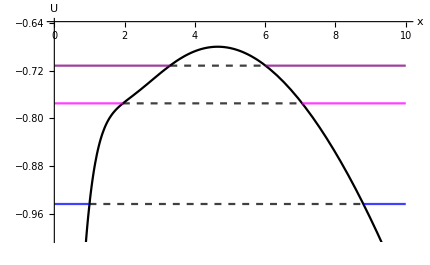

```mathematica
(*Show the potential and energy of the trajectories together*)
Potentialc7=Show[Uc7,Energyc7,ImageSize->{600,400},BaseStyle->{FontSize->14},PlotRange->{-1,-0.64}]
```

### Final Plot

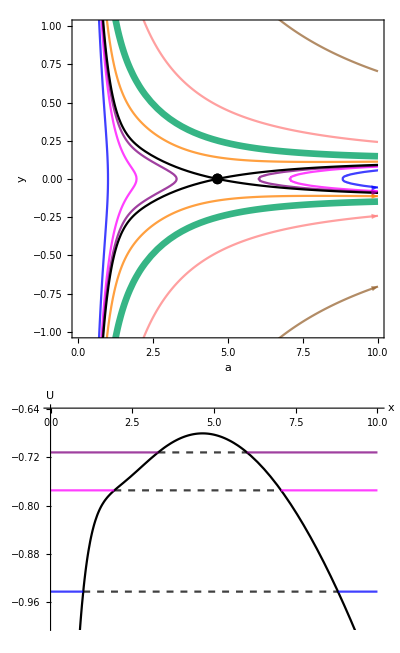

```mathematica
(*Plot the phase space and potential together*)
ayc7=GraphicsColumn[{PhaseSpacec7,Potentialc7},Spacings->{0,-20}]
```

```mathematica
(*Export["G:\\My Drive\\Wolfram Mathematica\\Project 1\\Non_Interacting_Matter\\Compact_Variables\\Full_Case\\x_Y_Z_R0.05\\Figures\\ay_Plots\\ayc7.pdf",ayc7]*)
```